#### Import MGenPackage

```mathematica
Block[{$Path=Append[$Path,NotebookDirectory[]]},
<<MGenPackage`]
```

#### Import MIDI

```mathematica
fileName=FileNameJoin[{NotebookDirectory[],"flute.mid"}];
```

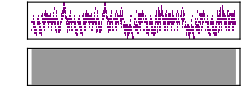

```mathematica
microsecondsPerQuarterNote=First@Cases[Flatten@Import[fileName,"Metadata"],("SetTempo"->x_)->x];
fluteSound=Import[fileName]
```

```mathematica
fluteSound[[1]]//Short[#,10]&
```

{SoundNote[B4,{0.9,1.09875},Piano,SoundVolume→0.807843],SoundNote[E5,{1.2,1.4525},Piano,SoundVolume→0.815686],SoundNote[E5,{1.8,2.0525},Piano,SoundVolume→0.831373],SoundNote[E5,{2.4,2.51625},Piano,SoundVolume→0.831373],«1055»,SoundNote[D#5,{191.85,192.},Piano,SoundVolume→0.784314],SoundNote[D#5,{192.,192.3},Piano,SoundVolume→0.784314],SoundNote[E5,{192.3,192.9},Piano,SoundVolume→0.784314]}

#### Transform to {note_number, start_ppq_in_bar, length_ppq, velocity_0_to_100}

Use EmbeddingLayer to embed integers

Make generator function that randomly selects a position in the song and forms pairs of 50 notes input and next {start_ppq_in_bar, note, length_ppq, velocity} as output.

TODO! Code output better so it can be formulated as softmax probabilities. Maybe {note, ppq_since_last_note, length_ppq, velocity}

```mathematica
SoundNote["B4",{0.9,1.0987500000000001},"Piano",SoundVolume->0.807843137254902]
```

SoundNote[B4,{0.9,1.09875},Piano,SoundVolume→0.807843]

#### Extract notes, position and length in 32nd notes

```mathematica
notes=fluteSound[[1]]/.SoundNote[note_,{start_,stop_},"Piano",SoundVolume->vel_]->{note,Round[1000000start/(microsecondsPerQuarterNote/8)],Max[1,Round[1000000(stop-start)/(microsecondsPerQuarterNote/8)]]};
notes//Short[#,20]&
```

{{B4,12,3},{E5,16,3},{E5,24,3},{E5,32,2},{G#5,34,2},{F#5,36,2},{E5,38,2},{D#5,40,2},{C#5,42,2},{B4,44,2},{A4,46,1},{B4,48,2},{E5,50,2},{D#5,52,2},{C#5,54,2},{B4,56,2},{A4,60,2},{B4,64,1},{A4,65,1},{B4,66,1},{A4,67,1},{G#4,68,4},{B4,76,4},{E5,80,2},{D#5,82,2},{E5,84,4},{F#5,88,1},{E5,89,1},{D#5,90,2},{E5,92,5},{G#5,98,2},{F#5,100,2},{E5,102,2},{D#5,104,2},{C#5,106,2},{B4,108,2},{A4,110,2},{B4,112,2},{E5,114,2},{D#5,116,2},{C#5,118,2},{B4,120,2},{A4,124,2},{B4,128,1},{A4,129,1},{B4,130,1},{A4,131,1},{G#4,132,4},{G#5,140,4},{F#5,144,2},«962»,{C#5,2446,2},{B4,2448,4},{C#5,2452,2},{D#5,2454,2},{E5,2456,2},{F#5,2458,2},{G#5,2460,2},{A5,2462,2},{B5,2464,9},{G#5,2474,2},{F#5,2476,2},{E5,2478,2},{D#5,2480,2},{C#5,2482,2},{B4,2484,2},{C#5,2486,2},{D#5,2488,2},{E5,2490,2},{F#5,2492,2},{G#5,2494,2},{A5,2496,9},{D#5,2506,2},{E5,2508,2},{F#5,2510,2},{G#5,2512,1},{E5,2514,2},{F#5,2516,2},{G#5,2518,2},{F#5,2520,1},{A5,2522,2},{G#5,2524,2},{F#5,2526,2},{E5,2528,2},{D#5,2530,2},{C#5,2532,2},{B4,2534,2},{C#5,2536,2},{D#5,2538,2},{E5,2540,2},{F#5,2542,2},{G#5,2544,2},{A5,2546,2},{B5,2548,2},{E5,2550,2},{G#5,2552,2},{F#5,2554,2},{E5,2556,2},{D#5,2558,2},{D#5,2560,4},{E5,2564,8}}

#### Transform to {note, 32nd notes to the next note, length in 32nd notes}. (‘ ‘ is no note)

```mathematica
notesDifferences=Transpose[{#[[1]],Differences[Join[#[[2]],{16+#[[2,-1]]}]],#[[3]]}&@Transpose[Join[{{" ",0,1}},notes]]];
notesDifferences//Short[#,10]&
```

{{ ,12,1},{B4,4,3},{E5,8,3},{E5,8,3},{E5,2,2},{G#5,2,2},{F#5,2,2},{E5,2,2},{D#5,2,2},{C#5,2,2},{B4,2,2},{A4,2,1},{B4,2,2},{E5,2,2},{D#5,2,2},{C#5,2,2},{B4,4,2},{A4,4,2},{B4,1,1},{A4,1,1},{B4,1,1},{A4,1,1},{G#4,8,4},{B4,4,4},{E5,2,2},{D#5,2,2},{E5,4,4},{F#5,1,1},{E5,1,1},«1005»,{D#5,2,2},{E5,2,2},{F#5,2,2},{G#5,2,1},{E5,2,2},{F#5,2,2},{G#5,2,2},{F#5,2,1},{A5,2,2},{G#5,2,2},{F#5,2,2},{E5,2,2},{D#5,2,2},{C#5,2,2},{B4,2,2},{C#5,2,2},{D#5,2,2},{E5,2,2},{F#5,2,2},{G#5,2,2},{A5,2,2},{B5,2,2},{E5,2,2},{G#5,2,2},{F#5,2,2},{E5,2,2},{D#5,2,2},{D#5,4,4},{E5,16,8}}

```mathematica
FromCharacterCode[#+46]&/@Range[0,88]
```

{.,/,0,1,2,3,4,5,6,7,8,9,:,;,<,=,>,?,@,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,[,\,],^,_,`,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,{,|,},~,.7f,.80,.81,.82,.83,.84,.85,.86}

#### Transform note string to a character

```mathematica
noteStrings=Flatten[Function[{octave},#<>ToString[octave]&/@{"A","A#","B","C","C#","D","D#","E","F","F#","G","G#"}]/@{1,2,3,4,5,6,7}]~Join~{" "}
```

{A1,A#1,B1,C1,C#1,D1,D#1,E1,F1,F#1,G1,G#1,A2,A#2,B2,C2,C#2,D2,D#2,E2,F2,F#2,G2,G#2,A3,A#3,B3,C3,C#3,D3,D#3,E3,F3,F#3,G3,G#3,A4,A#4,B4,C4,C#4,D4,D#4,E4,F4,F#4,G4,G#4,A5,A#5,B5,C5,C#5,D5,D#5,E5,F5,F#5,G5,G#5,A6,A#6,B6,C6,C#6,D6,D#6,E6,F6,F#6,G6,G#6,A7,A#7,B7,C7,C#7,D7,D#7,E7,F7,F#7,G7,G#7, }

```mathematica
fromNoteString[str_]:=If[str==" "," ",FromCharacterCode[First[First[Position[noteStrings,str]]]+44]]
fromNoteString/@noteStrings
```

{-,.,/,0,1,2,3,4,5,6,7,8,9,:,;,<,=,>,?,@,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,[,\,],^,_,`,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,{,|,},~,.7f,.80, }

```mathematica
fromNoteCharacter[ch_]:=If[ch==" "," ",noteStrings[[First[ToCharacterCode[ch]]-44]]]
fromNoteCharacter/@fromNoteString/@noteStrings==noteStrings
```

True

```mathematica
notesWithCharacters=Transpose[{fromNoteString/@#[[1]],#[[2]],#[[3]]}&@Transpose[notesDifferences]];
notesWithCharacters//Short[#,10]&
```

{{ ,12,1},{S,4,3},{d,8,3},{d,8,3},{d,2,2},{h,2,2},{f,2,2},{d,2,2},{c,2,2},{a,2,2},{S,2,2},{Q,2,1},{S,2,2},{d,2,2},{c,2,2},{a,2,2},{S,4,2},{Q,4,2},{S,1,1},{Q,1,1},{S,1,1},{Q,1,1},{\,8,4},{S,4,4},{d,2,2},{c,2,2},{d,4,4},{f,1,1},{d,1,1},{c,2,2},{d,6,5},{h,2,2},{f,2,2},{d,2,2},«996»,{d,2,2},{f,2,2},{h,2,2},{],10,9},{c,2,2},{d,2,2},{f,2,2},{h,2,1},{d,2,2},{f,2,2},{h,2,2},{f,2,1},{],2,2},{h,2,2},{f,2,2},{d,2,2},{c,2,2},{a,2,2},{S,2,2},{a,2,2},{c,2,2},{d,2,2},{f,2,2},{h,2,2},{],2,2},{_,2,2},{d,2,2},{h,2,2},{f,2,2},{d,2,2},{c,2,2},{c,4,4},{d,16,8}}

#### Make sure notes don’t overlap

```mathematica
notesWithCharactersNoOverlap={#[[1]],#[[2]],Min[#[[2]],#[[3]]]}&/@notesWithCharacters;
notesWithCharactersNoOverlap//Short[#,10]&
```

{{ ,12,1},{S,4,3},{d,8,3},{d,8,3},{d,2,2},{h,2,2},{f,2,2},{d,2,2},{c,2,2},{a,2,2},{S,2,2},{Q,2,1},{S,2,2},{d,2,2},{c,2,2},{a,2,2},{S,4,2},{Q,4,2},{S,1,1},{Q,1,1},{S,1,1},{Q,1,1},{\,8,4},{S,4,4},{d,2,2},{c,2,2},{d,4,4},{f,1,1},{d,1,1},{c,2,2},{d,6,5},{h,2,2},{f,2,2},{d,2,2},«996»,{d,2,2},{f,2,2},{h,2,2},{],10,9},{c,2,2},{d,2,2},{f,2,2},{h,2,1},{d,2,2},{f,2,2},{h,2,2},{f,2,1},{],2,2},{h,2,2},{f,2,2},{d,2,2},{c,2,2},{a,2,2},{S,2,2},{a,2,2},{c,2,2},{d,2,2},{f,2,2},{h,2,2},{],2,2},{_,2,2},{d,2,2},{h,2,2},{f,2,2},{d,2,2},{c,2,2},{c,4,4},{d,16,8}}

#### Transform to: New note is note character, same note on next 32nd step is ‘+‘, rest on the next 32nd step is ‘ ‘.

```mathematica
stringCodedNotes=StringJoin@Flatten[Module[{},{#[[1]],Array["+"&,#[[3]]-1],Array[" "&,#[[2]]-#[[3]]]}]&/@notesWithCharacters]
```

S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S+++d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    h+++f+]+h+f+h+d+c+d+f+d+c+a+S+a+c+d+f+]+h+f+h+d+_+++]h]hf+++    f++ h+d+f+h+]+h+f+d+a+d+c+f+d+h+f+d+f+d+f+h+]+h+f+d+S+c+a+d+c+f+d+c+fdc+d+++++h+f+d+^+h+f+d+m+  d+  c+d+f+S+c+a+S+R+S+_+^+h+f++ d++ c f+d+c+a d+c+a+S+R+S++ aSR+S++++ c+a+S+a+c+d+f+h+f+h++ ]hf+h+++++_+^+h+^+_+m+o+p+o+p++ om_+m+++_^h+^+++g++++++++ f+d+c+a+S+R+S e+++f+++++d+c+a+c S+a+c+d+h+f+d+f _+^+h+f+d+c+a+S++++++++   S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S+++d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    h+++f+]+h+f+h+d+c+d+f+d+c+a+S+a+c+d+f+]+h+f+h+d+_+++]h]hf+++    f++ h+d+f+h+]+h+f+d+a+d+c+f+d+h+f+d+f+d+f+h+]+h+f+d+S+c+a+d+c+f+d+c+fdc+d+++++h+f+d+^+h+f+d+m+  d+  c+d+f+S+c+a+S+R+S+_+^+h+f++ d++ c f+d+c+a d+c+a+S+R+S++ aSR+S++++ c+a+S+a+c+d+f+h+f+h++ ]hf+h+++++_+^+h+^+_+m+o+p+o+p++ om_+m+++_^h+^+++g++++++++ f+d+c+a+S+R+S e+++f+++++d+c+a+c S+a+c+d+h+f+d+f _+^+h+f+d+c+a+S++++++++   S++ f+++    f+++    f ]+h+f+d+c+a+S+_ d+c+d+f+]+h+f+h++ d++     c++ h+++    h+++    h _+]+h+f+e+c+a+m f+e+f+h+_+]+h+]+  f+      a++ b a+b+d+b+a+S+Q+\+S+Q+a+S+b+a+S+a S+a+b+a+S+Q+\+Z+Q+\+S+Q+a+S+Q+S+Q+S++++ b+a+S+e+b+a+S h++ S++ Q+S+a Z Q+  \+  Z++++++     a++ c f+d+c+d a+S+a+b S+b+f+_ b+a+S+a d+b+a+b S+Q+S+a Q+a+d+] h+f+d+c f+h+]+a f+h+]+S+a+c+d+f+h+]+h h d ] d _+  ] h ]h]hf++     S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S++ d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    S++ a Q+\+Q+S+a+c+d+f+h+]+_+] h f d c S+R+S+a+c+d+f+h+]+_+m+_ ] h f d a+S+a+c+d+f+h+]+_+m+n+m _ ] h f _+]+h+]+h+f+d+c h+f+d+f+d+c+a+S+++a+c+d+f+h+]+_++++++++ h+f+d+c+a+S+a+c+d+f+h+]++++++++ c+d+f+h d+f+h+f ]+h+f+d+c+a+S+a+c+d+f+h+]+_+d+h+f+d+c+c+++d+++++++S++ f+++    f+++    f ]+h+f+d+c+a+S+_ d+c+d+f+]+h+f+h++ d++     c++ h+++    h+++    h _+]+h+f+e+c+a+m f+e+f+h+_+]+h+]+  f+      a++ b a+b+d+b+a+S+Q+\+S+Q+a+S+b+a+S+a S+a+b+a+S+Q+\+Z+Q+\+S+Q+a+S+Q+S+Q+S++++ b+a+S+e+b+a+S+h++ S++ Q+S+a Z Q+  \+  Z++++++     a++ c f+d+c+d a+S+a+b S+b+f+_ b+a+S+a d+b+a+b S+Q+S+a Q+a+d+] h+f+d+c f+h+]+a f+h+]+S+a+c+d+f+h+]+h h d ] d _+  ] h ]h]hf++     S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S++ d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    S++ a Q+\+Q+S+a+c+d+f+h+]+_+] h f d c S+R+S+a+c+d+f+h+]+_+m+_ ] h f d a+S+a+c+d+f+h+]+_+m+n+m _ ] h f _+]+h+]+h+f+d+c h+f+d+f+d+c+a+S+++a+c+d+f+h+]+_++++++++ h+f+d+c+a+S+a+c+d+f+h+]++++++++ c+d+f+h d+f+h+f ]+h+f+d+c+a+S+a+c+d+f+h+]+_+d+h+f+d+c+c+++d+++++++

#### Make function that does conversion from MIDI Sound object to string

```mathematica
fromMIDIFileToCodedNoteString[fileName_String]:=Module[{microsecondsPerQuarterNote,midiSound,notes,notesDifferences,noteStrings,notesWithCharacters,notesWithCharactersNoOverlap,stringCodedNotes},
microsecondsPerQuarterNote=First@Cases[Flatten@Import[fileName,"Metadata"],("SetTempo"->x_)->x];
midiSound=Import[fileName];
notes=midiSound[[1]]/.SoundNote[note_,{start_,stop_},instrument_,SoundVolume->vel_]->{note,Round[1000000start/(microsecondsPerQuarterNote/8)],Max[1,Round[1000000(stop-start)/(microsecondsPerQuarterNote/8)]]};
notesDifferences=Transpose[{#[[1]],Differences[Join[#[[2]],{64+#[[2,-1]]}]],#[[3]]}&@Transpose[Join[{{" ",0,1}},notes]]];
noteStrings=Flatten[Function[{octave},#<>ToString[octave]&/@{"A","A#","B","C","C#","D","D#","E","F","F#","G","G#"}]/@{1,2,3,4,5,6,7}]~Join~{" "};
notesWithCharacters=Transpose[{fromNoteString/@#[[1]],#[[2]],#[[3]]}&@Transpose[notesDifferences]];
notesWithCharactersNoOverlap={#[[1]],#[[2]],Min[#[[2]],#[[3]]]}&/@notesWithCharacters;
stringCodedNotes=StringJoin@Flatten[Module[{},{#[[1]],Array["+"&,#[[3]]-1],Array[" "&,#[[2]]-#[[3]]]}]&/@notesWithCharacters]
]
```

```mathematica
fromMIDIFileToCodedNoteString[fileName]
```

S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S+++d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    h+++f+]+h+f+h+d+c+d+f+d+c+a+S+a+c+d+f+]+h+f+h+d+_+++]h]hf+++    f++ h+d+f+h+]+h+f+d+a+d+c+f+d+h+f+d+f+d+f+h+]+h+f+d+S+c+a+d+c+f+d+c+fdc+d+++++h+f+d+^+h+f+d+m+  d+  c+d+f+S+c+a+S+R+S+_+^+h+f++ d++ c f+d+c+a d+c+a+S+R+S++ aSR+S++++ c+a+S+a+c+d+f+h+f+h++ ]hf+h+++++_+^+h+^+_+m+o+p+o+p++ om_+m+++_^h+^+++g++++++++ f+d+c+a+S+R+S e+++f+++++d+c+a+c S+a+c+d+h+f+d+f _+^+h+f+d+c+a+S++++++++   S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S+++d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    h+++f+]+h+f+h+d+c+d+f+d+c+a+S+a+c+d+f+]+h+f+h+d+_+++]h]hf+++    f++ h+d+f+h+]+h+f+d+a+d+c+f+d+h+f+d+f+d+f+h+]+h+f+d+S+c+a+d+c+f+d+c+fdc+d+++++h+f+d+^+h+f+d+m+  d+  c+d+f+S+c+a+S+R+S+_+^+h+f++ d++ c f+d+c+a d+c+a+S+R+S++ aSR+S++++ c+a+S+a+c+d+f+h+f+h++ ]hf+h+++++_+^+h+^+_+m+o+p+o+p++ om_+m+++_^h+^+++g++++++++ f+d+c+a+S+R+S e+++f+++++d+c+a+c S+a+c+d+h+f+d+f _+^+h+f+d+c+a+S++++++++   S++ f+++    f+++    f ]+h+f+d+c+a+S+_ d+c+d+f+]+h+f+h++ d++     c++ h+++    h+++    h _+]+h+f+e+c+a+m f+e+f+h+_+]+h+]+  f+      a++ b a+b+d+b+a+S+Q+\+S+Q+a+S+b+a+S+a S+a+b+a+S+Q+\+Z+Q+\+S+Q+a+S+Q+S+Q+S++++ b+a+S+e+b+a+S h++ S++ Q+S+a Z Q+  \+  Z++++++     a++ c f+d+c+d a+S+a+b S+b+f+_ b+a+S+a d+b+a+b S+Q+S+a Q+a+d+] h+f+d+c f+h+]+a f+h+]+S+a+c+d+f+h+]+h h d ] d _+  ] h ]h]hf++     S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S++ d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    S++ a Q+\+Q+S+a+c+d+f+h+]+_+] h f d c S+R+S+a+c+d+f+h+]+_+m+_ ] h f d a+S+a+c+d+f+h+]+_+m+n+m _ ] h f _+]+h+]+h+f+d+c h+f+d+f+d+c+a+S+++a+c+d+f+h+]+_++++++++ h+f+d+c+a+S+a+c+d+f+h+]++++++++ c+d+f+h d+f+h+f ]+h+f+d+c+a+S+a+c+d+f+h+]+_+d+h+f+d+c+c+++d+++++++S++ f+++    f+++    f ]+h+f+d+c+a+S+_ d+c+d+f+]+h+f+h++ d++     c++ h+++    h+++    h _+]+h+f+e+c+a+m f+e+f+h+_+]+h+]+  f+      a++ b a+b+d+b+a+S+Q+\+S+Q+a+S+b+a+S+a S+a+b+a+S+Q+\+Z+Q+\+S+Q+a+S+Q+S+Q+S++++ b+a+S+e+b+a+S+h++ S++ Q+S+a Z Q+  \+  Z++++++     a++ c f+d+c+d a+S+a+b S+b+f+_ b+a+S+a d+b+a+b S+Q+S+a Q+a+d+] h+f+d+c f+h+]+a f+h+]+S+a+c+d+f+h+]+h h d ] d _+  ] h ]h]hf++     S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S++ d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    S++ a Q+\+Q+S+a+c+d+f+h+]+_+] h f d c S+R+S+a+c+d+f+h+]+_+m+_ ] h f d a+S+a+c+d+f+h+]+_+m+n+m _ ] h f _+]+h+]+h+f+d+c h+f+d+f+d+c+a+S+++a+c+d+f+h+]+_++++++++ h+f+d+c+a+S+a+c+d+f+h+]++++++++ c+d+f+h d+f+h+f ]+h+f+d+c+a+S+a+c+d+f+h+]+_+d+h+f+d+c+c+++d+++++++

#### Make function that converts from string back to Sound object. Listen.

```mathematica
fromCodedNoteString[noteString_,tempoBPM_]:=Module[{note32ToTime},
note32ToTime[notes32_]:=60. notes32/8 /tempoBPM;
Sound[SoundNote[#[[1]],#[[2]],"Flute"]&/@StringCases[noteString,{
(x:(" "..)):>{None,note32ToTime@StringLength[x]},
(x:(Except[Characters[" +"]]~~"+"...)):>{fromNoteCharacter@StringTake[x,{1}],note32ToTime@StringLength[x]}
}]]
]
```

```mathematica
fromCodedNoteString[stringCodedNotes,120]
```

#### Convert to coded string and back

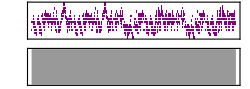

```mathematica
fromCodedNoteString[fromMIDIFileToCodedNoteString[fileName],100]
```

#### Construct a LSTM net with 4 layers and 320 neurons in each layer or smaller

```mathematica
sampleText[text_,len_,num_]:=Module[
{positions=RandomInteger[{len+1,StringLength[text]-1},num]},
Thread[StringTake[text,{#-len,#}&/@positions]->StringPart[text,positions+1]]]
```

```mathematica
text=fromMIDIFileToCodedNoteString[fileName];
```

```mathematica
trainingData=sampleText[text,50,10000];
RandomSample[trainingData,5]
```

{f+_ b+a+S+a d+b+a+b S+Q+S+a Q+a+d+] h+f+d+c f+h+]+a→ ,+]+_++++++++ h+f+d+c+a+S+a+c+d+f+h+]++++++++ c+d+f+→h,+R+S+a+c+d+f+h+]+_+m+_ ] h f d a+S+a+c+d+f+h+]+_+m+→n,n+m _ ] h f _+]+h+]+h+f+d+c h+f+d+f+d+c+a+S+++a+c+d→+,f+h+]+_+m+_ ] h f d a+S+a+c+d+f+h+]+_+m+n+m _ ] h f→ }

```mathematica
characters=Union[Characters[text]]
```

{^,_,+,],\, ,a,b,c,d,e,f,g,h,m,n,o,p,Q,R,S,Z}

```mathematica
net=NetInitialize@NetChain[{
UnitVectorLayer[],
LongShortTermMemoryLayer[300,"Dropout"->0.2],
LongShortTermMemoryLayer[300],
LongShortTermMemoryLayer[300],
LongShortTermMemoryLayer[300],
SequenceLastLayer[],
LinearLayer[64],
Tanh,
LinearLayer[],
SoftmaxLayer[]},
"Input"->NetEncoder[{"Characters",characters}],
"Output"->NetDecoder[{"Class",characters}]
]
```

NetChain[]

#### Train the network (with checkpoints)

```mathematica
trainedNet=net;
```

```mathematica
trainedNet=NetTrain[trainedNet,trainingData,BatchSize->512,TargetDevice->"CPU",MaxTrainingRounds->Quantity[8,"Hours"],TrainingProgressCheckpointing->{"Directory","~/Desktop/slask/FluteCheckpoints"}]
```

NetChain[]

#### Listen to the results

```mathematica
generate[net_,start_,len_]:=
Nest[StringJoin[#,net[#]]&,start,len]
```

```mathematica
trainedNet=Import[FileNameJoin[{NotebookDirectory[],"FluteNets","2017-09-20T22:51:53_2_286_5718_4.66e-3.wlnet"}]]
```

NetChain[]

```mathematica
generated=generate[trainedNet,"+c+a+S+R+S e+++f+++++",200]
```

+c+a+S+R+S e+++f+++++c+a+c S+a+c+d+h+f+d+f _+^+h+f+d+c+a+S++++++++   S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S++ d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    S++ d+c+d+++fdc+d++++ h+

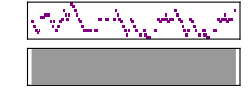

```mathematica
fromCodedNoteString[generated,100]
```

```mathematica
generateSample[net_,start_,len_]:=
Nest[StringJoin[#,net[#,"RandomSample"]]&,start,len]
generateSampleTruncated[net_,start_,len_]:=
Nest[StringJoin[#,net[StringTake[#,-Min[250,StringLength[#]]],"RandomSample"]]&,start,len]
```

```mathematica
sampled=generateSample[trainedNet,"+c+a+S+R+S e+++f+++++",200]
```

+c+a+S+R+S e+++f+++++c+a+c S+a+c+d+h+f+d+f _+^+h+f+d+c+a+S++++++++   S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    h+++f+^+h+f+h+d+c+d+f+d+c+a+S+a+c+d+f+]+h+f+h+d+_+++    c++ h+++    h+++    h _+]+h+f+e+

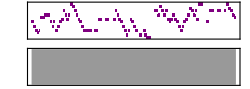

```mathematica
fromCodedNoteString[sampled,100]
```

```mathematica
Export["/tmp/a.mid",%]
```

/tmp/a.mid

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["/tmp/a.mid"]]]
```

#### Result: trainedNet was over trained and just learned the entire piece

```mathematica
toWAVSound[sound_Sound]:=ImportString[ExportString[sound,"WAV"],"WAV"]
```